```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

```mathematica
fit=A/((x-X)^2+b^2)/.{A->"4.2780000"×10^("7"),X->408.4,b->54.25};
center=408.4(*the lorentzian center*)
```

408.4

```mathematica
lorentzian=Flatten[Import["lorentzian.csv","Table"]];
```

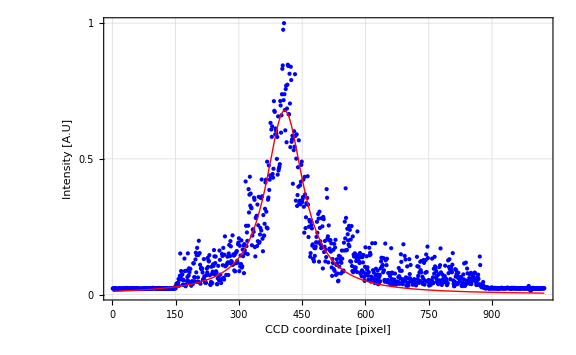

```mathematica
plot=Show[{ListPlot[lorentzian,PlotRange->All,PlotStyle->{Blue,PointSize[Medium]}],Plot[fit,{x,1,1024},PlotStyle->{Red,Thick(*ness[0.005]*)},PlotRange->All]},Frame->True,GridLines->Automatic,FrameLabel->{{"Intensity\n[A.U]",None},{"CCD coordinate [pixel]","Wavelength [nm]"}}
,FrameTicks->{{{0,{Max[lorentzian],1},{Max[lorentzian]/2,0.5}},None},{Automatic,Append[Drop[Table[{center+j,NumberForm[653.3+1/30 j,4]},{j,-400,630,center/2}],{3}],{center,656.3}]}}
,LabelStyle->Directive[(*Bold,*)Black, 25],ImageSize->Large]
```

```mathematica
Append[Drop[Table[{center+j,NumberForm[653.3+1/30 j,4]},{j,-400,630,center/2}],{3}],{center,656.3}]
```

{{8.4,640.},{212.6,646.8},{621.,660.4},{825.2,667.2},{1029.4,674.},{408.4,656.3}}

```mathematica
Export["sample-lorentzian.pdf",plot]
Export["sample-lorentzian.png",plot]
```

sample-lorentzian.pdf

sample-lorentzian.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sample-lorentzian.png"]]]
```